# Individual-based modeling of COVID-19 transmission in college communities

### D. Gurarie, Q. Huang, A. Tsoi Department of Mathematics, Applied Mathematics and Statistics, Case Western Reserve University, Cleveland, OH, USA, 44106.

### Reference

## 1. Q. Huang, M. Ndeffo-Mbah, A. Mondal, S. Lee, D. Gurarie, Individual-based modeling of COVID-19 transmission in college communities, Preprint in medRxiv

## Model setup

An individual - based model (IBM) for COVID - 19 transmission in college communities  [1] was developed. Two basic components of college IBM include: (1) college community and its social interaction patterns and (2) infection transmission and disease progress.

Key Inputs to generate a synthetic college community. 
1. student body
2. class list with enrollment weights, and weekly schedule
3. Enrollment /student (e.g. 3 classes)
Outputs: Class seat association with schedule
Class = {“MWF”,<|{1,2}->S116, {1,5}->S222,...|>}
Code: students draw classes randomly from the weighted class pool (class lottery)

Disease states SIR: 0,1,2
In-host state: {i, d, “Path”} 
Deterministic progress: {i, d, “Path”} -> {i +UnitStep[i,d-L[“Path”]],d+1,“Path”}
“Path” = {A,S}
L[A]=12; L[S]=21

### Key Description

Social mixing: scheduled (e.g., classes, dorm) and random contacts (e.g., dining, social). 
Disease progression. The infection stages are classified as susceptible (S), infected (I), and recovered (R) stages. Once infected, each individual undergoes a prescribed infection progress pattern determined by stage duration and time. We partition the host population into asymptomatic and symptomatic groups.

## Model Codes

```mathematica
(*Disease Labels*)Slab={"S","I","R"};
(*Week days*)
Week={"M","T","W","R","F","S","U"};
(*Time range made of weekdays*)
WeR[n_]:=Join@@Table[Week,{n}]
```

#### Social mixing

Patterns:
1) Partition of total host-pool (HP) into nonoverlapping random pools of sizes m <# <n
2) Pool-size distribution: 
size | m1 | ... | mk
frequency | f1 | ... | fk ; f1+f2+...+fk=1
Generate overlapping random pools of sizes {m1,m2,...} with per-host frequences {f1,f2,...}
Men contact rate/day: f1*m1(m1-1)+f2*m2(m2-1)+...

```mathematica
(*Nonoverlapping partition of pool hp into clusters clus={f1,f2,...}->{m1, m2,...}, with weights/frequencies sum[fi]=1*)
RanMixN[hp_,clus_]:=
Block[{L=Length@hp,(*mean pool size*)mps=Dot@@clus,mm},
(*allow 1 contact/host/day on average*)mm=RandomChoice[clus,Floor[L/mps]];
TakeList[RandomSample@hp,UpTo/@mm]]
(*Random overlapping clusters of hp based on weighted cluster clus={f1,f2,...}->{m1, m2,...},and mean intensity of social mixing = om*)
RanMixC[hp_,clus_,om_]:=
Block[{L=Length@hp,(*mean pool size*)mps=Dot@@clus,mm},
mm=RandomChoice[clus,Floor[om L/mps]];
RandomSample[hp,#]&/@mm]
```

```mathematica
(*Non-overlapping social mixing: relative weights = wec, contact pool sizes = conS*)
MixP[wec_,conS_]:=(wec conS)/(Total@(wec conS))->conS
```

```mathematica
(*Mean contact rate*)
MCR[ww_->cc_]:=(ww.(cc(cc-1)))/(Total@ww)
```

#### Disease progress/recovery for I-pool

```mathematica
(*I-Progress*)ProG[{1,d_,pw_}]:={1,d+1,pw};
(*I-Recovery*)ReC[{1,d_,pw_}]:={2,pw};
```

```mathematica
(*S-progress: state c={0,pw}+ infection Bernoulli step p=0 or p=1. If p=0 (no infection) or p -absent (no contact), c->c; if p=1 (infection S->I) c={0,pathawy}->{1, 0, Pathway}*)
SProgF[{c_,1}]:=Prepend[c,1]
SProgF[{c_,p_}]:=c
SProgF[{c_}]:=c
```

```mathematica
(*Bernoulli probability f-n for transitions: E->I->...->R, in terms of stage duration = x*)
ϕ[x_,m_]=x^m/(1+x^m);
(*Disease progress as f-n of probability of infection =a, for S-state*)
RanBernDraw[a_]:=RandomVariate[BernoulliDistribution@a]
SetAttributes[RanBernDraw,Listable]
```

#### Infectivity function for I

```mathematica
(*Basic infectivity profile*)
BiF[x_,p_]=x^p Exp[p(1-x)];
```

```mathematica
inF[Missing[__]]=0;
inF[{0,___}]=0;
inF[{2,___}]=0;
inF[{1,d_,pw_}]:=(*max infectivity*)maxI[pw](*temporal pattern*)BiF[3 d/L[pw],(*Steepness*)stp[pw]]
(*Max infectivity*)
{maxI["A"],maxI["S"]}={.2,.25};
{L["A"],L["S"]}={12,21};
(*Infection function steepness*){stp["A"],stp["S"]}={4,5};
```

Alternative: in-host state {i,d,L}, host-specific

#### Probability of S-survival in class/ dorm

```mathematica
(*CR seat spacing for neigbour pool b of seat a*)
Eud[a_,b_]:=EuclideanDistance[a,#]&/@b;
(*prob of S-survival in class for 'seating association'=seat, and work-pool student association wpS*)
PrS[seat_,wpS_,aC_,(*classroom spread distance scale [m]*)d_]:=
Block[{g1=NearestNeighborGraph[Keys@seat,{All,d}],Svic,dRA,inS,StI,Spo,dsI},
(*seat vicinity*)Svic=AssociationMap[AdjacencyList[g1,#]&,VertexList@g1];
(*seat distance risk*)dRA=KeyValueMap[#->E^(- Eud[##]/d)&,Svic];
(*extract infection states*)inS=KeyTake[wpS,Values@seat];
(*seat->infection status assos*)StI=inS/@seat;
(*S-pool*)Spo=Keys@Select[StI,#[[1]]==0&];
(*distance-infectivity*)
dsI=Merge[
{(*distance factors*)dRA,
(*infectivity levels*)Map[inF/@StI,Svic,{2}]},
Times@@(1-aC Times@@#)&];
(*Survival for S-pool from seat->risk*)
KeyMap[seat,KeyTake[dsI,Spo]]]
(*Probability of survival in S for housing unit association = huA*)
PrH[huA_,(*S-pool*)spo_,(*EI-pool*)eip_,(*individual and/or environmental protection factor*)a_]:=
Block[
{z0=KeyTake[spo,huA],
z1=(*infected*)KeyTake[eip,huA],
(*prob of survival*)prs},
 prs=Times@@(1-a inF/@z1);
prs&/@z0]
```

Prob of survival:
S contacts have infectivity {b1,b2,...}, environmental risk {aC,aD,aS}
(1- a1*b1)(1-a2*b2)...

#### Plot infectivity

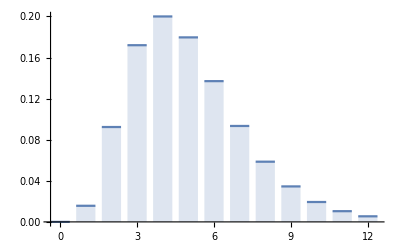

```mathematica
DiscretePlot[inF[{1,d,"A"}],{d,0,12},ExtentSize->0.75]
```

## Generate a synthetic college community

Setup
1) two types of weekly schedule: MWF (1-hour), TuTh (1.5 - hour)
2) daily time periods: 7 nonoverlapping MWF periods (M1,M2,...), 5 nonoverlapping TuTh periods (T1,T2,...)
3) Two student bodies and classes: FS (freshman-sophomore, e.g. 60%), JS (junior senior, 40%), each group taking its own classes (no class mixing)
4) for each group maintain its mean class size,  MCS=(#students*(#classes/student =3))/(#classes) => (#classes) NC=(#students*(#classes/student =3))/MCM
5) For each FS/ JS - class assign its preference weight in the range [1,5], for class selection
6) Each  (FS, JS)-class is assigned weekly schedule (MWF or TuTh) and time period (Mi or Ti). The latter is only important for scheduling, not for outbreak code.
7) Scheduling: randomly sorted students of each pool draw randomly 3 classes from their weighted class-list (FS,JS), avoiding daily time-overlap

### Classroom seating

This codes generate random or near optimal seating for a rectangular classroom (n x m), and a student pool (sP < n*m),

```mathematica
(*Classroom type *)
CRType[n_,m_]:=Tuples[{Range[n],Range[m]}];
(*Random seating*)
RanSeat[(*room*)cR_,(*list*)sP_]:=
AssociationThread[RandomSample[cR,Min[Length@sP,Length@cR]],sP]
OpSeat[(*room*)cR_,(*distance of spread [units of chair spacing]*)d_,(*student pool*)sP_]:=
Block[{nS=Length@sP,cS,cm,ass},
(*Initialize*)cS={Round[cR[[-1]]/2]};
Do[If[Length@cS<nS(*pool size*),
cm=Complement[cR,cS];
ass=Sort[Total[E^-#]&/@AssociationMap[Nearest[cS->"Distance",#,{All,d}]&,cm]];
AppendTo[cS,First@Keys@ass]],{nS}];
AssociationThread[cS,sP]]
(*Seat association for class name cn, based on 20% excess capacity, selected from classroom types Crt*)
SeatAs[cn_,Crt_]:=
Block[{cL=CombCE@cn,cr},
cr=SelectFirst[Crt,Length[#]>1.2 Length@cL&];
OpSeat[cr,2,cL]]
```

```mathematica
(*Plot classroom seating*)
PloC[(*room*)cR_,(*seat assos*)sa_,op___]:=
Graphics[{Circle[#,.2]&/@cR,{Red,Disk[#,.2]&/@Keys@sa}},op]
```

### Basic class-schedule codes and inputs

Daily periods labels: 0,1,...6 (MWF); 0,1,..,4 (TR)

```mathematica
(*Weekly day schedule: weights ->  types*)
WeekS=(*weights*){3,2}->{{"M","W","F"},{"T","R"}};
(*uniform class weight assignment function for class list cL, in the range [a,b]*)
ClassWeight[cL_,a_,b_]:=AssociationThread[FCList,Round[a+(b-a)/(Length@cL)Range[Length@cL]]]
(*Weekly-daily schedule assignment for class list cL*)
ClassWeekDaySched[cL_]:=
Block[
{zz=AssociationMap[RandomChoice[WeekS]&,cL],gz,gm,gt,tm,tt},
(*group classes by WeekS={MWF,TR}*)gz=Keys/@GroupBy[zz,#&];
(*Select MWF,TR*)gm=gz@{"M","W","F"};gt=gz@{"T","R"};(*assign time slot*)tm=Mod[#[[1]],7]&/@PositionIndex[gz@{"M","W","F"}];tt=Mod[#[[1]],5]&/@PositionIndex[gz@{"T","R"}];Merge[{zz,tm,tt},#&]]
```

### Set up class and student schedules for FS student body

```mathematica
(*Single student body, FS*)
StuF="S"<>ToString@#&/@Range@(nF=2400);
```

```mathematica
(*FS class list, for MCS=60, roster names FC*)
FCList=
With[{nc=Round[(nF 3(*classes/student*))/(50(*MCS*))]},
Table[Subscript[SC, i],{i,nc}]]
```

{SC_1,SC_2,SC_3,SC_4,SC_5,SC_6,SC_7,SC_8,SC_9,SC_10,SC_11,SC_12,SC_13,SC_14,SC_15,SC_16,SC_17,SC_18,SC_19,SC_20,SC_21,SC_22,SC_23,SC_24,SC_25,SC_26,SC_27,SC_28,SC_29,SC_30,SC_31,SC_32,SC_33,SC_34,SC_35,SC_36,SC_37,SC_38,SC_39,SC_40,SC_41,SC_42,SC_43,SC_44,SC_45,SC_46,SC_47,SC_48,SC_49,SC_50,SC_51,SC_52,SC_53,SC_54,SC_55,SC_56,SC_57,SC_58,SC_59,SC_60,SC_61,SC_62,SC_63,SC_64,SC_65,SC_66,SC_67,SC_68,SC_69,SC_70,SC_71,SC_72,SC_73,SC_74,SC_75,SC_76,SC_77,SC_78,SC_79,SC_80,SC_81,SC_82,SC_83,SC_84,SC_85,SC_86,SC_87,SC_88,SC_89,SC_90,SC_91,SC_92,SC_93,SC_94,SC_95,SC_96,SC_97,SC_98,SC_99,SC_100,SC_101,SC_102,SC_103,SC_104,SC_105,SC_106,SC_107,SC_108,SC_109,SC_110,SC_111,SC_112,SC_113,SC_114,SC_115,SC_116,SC_117,SC_118,SC_119,SC_120,SC_121,SC_122,SC_123,SC_124,SC_125,SC_126,SC_127,SC_128,SC_129,SC_130,SC_131,SC_132,SC_133,SC_134,SC_135,SC_136,SC_137,SC_138,SC_139,SC_140,SC_141,SC_142,SC_143,SC_144}

```mathematica
(*Weight assignment*)
FCweight=ClassWeight[FCList,4,10]
```

<|SC_1→4,SC_2→4,SC_3→4,SC_4→4,SC_5→4,SC_6→4,SC_7→4,SC_8→4,SC_9→4,SC_10→4,SC_11→4,SC_12→4,SC_13→5,SC_14→5,SC_15→5,SC_16→5,SC_17→5,SC_18→5,SC_19→5,SC_20→5,SC_21→5,SC_22→5,SC_23→5,SC_24→5,SC_25→5,SC_26→5,SC_27→5,SC_28→5,SC_29→5,SC_30→5,SC_31→5,SC_32→5,SC_33→5,SC_34→5,SC_35→5,SC_36→6,SC_37→6,SC_38→6,SC_39→6,SC_40→6,SC_41→6,SC_42→6,SC_43→6,SC_44→6,SC_45→6,SC_46→6,SC_47→6,SC_48→6,SC_49→6,SC_50→6,SC_51→6,SC_52→6,SC_53→6,SC_54→6,SC_55→6,SC_56→6,SC_57→6,SC_58→6,SC_59→6,SC_60→6,SC_61→7,SC_62→7,SC_63→7,SC_64→7,SC_65→7,SC_66→7,SC_67→7,SC_68→7,SC_69→7,SC_70→7,SC_71→7,SC_72→7,SC_73→7,SC_74→7,SC_75→7,SC_76→7,SC_77→7,SC_78→7,SC_79→7,SC_80→7,SC_81→7,SC_82→7,SC_83→7,SC_84→8,SC_85→8,SC_86→8,SC_87→8,SC_88→8,SC_89→8,SC_90→8,SC_91→8,SC_92→8,SC_93→8,SC_94→8,SC_95→8,SC_96→8,SC_97→8,SC_98→8,SC_99→8,SC_100→8,SC_101→8,SC_102→8,SC_103→8,SC_104→8,SC_105→8,SC_106→8,SC_107→8,SC_108→8,SC_109→9,SC_110→9,SC_111→9,SC_112→9,SC_113→9,SC_114→9,SC_115→9,SC_116→9,SC_117→9,SC_118→9,SC_119→9,SC_120→9,SC_121→9,SC_122→9,SC_123→9,SC_124→9,SC_125→9,SC_126→9,SC_127→9,SC_128→9,SC_129→9,SC_130→9,SC_131→9,SC_132→10,SC_133→10,SC_134→10,SC_135→10,SC_136→10,SC_137→10,SC_138→10,SC_139→10,SC_140→10,SC_141→10,SC_142→10,SC_143→10,SC_144→10|>

```mathematica
(*Random class schedule*)
FCsched=(SeedRandom["FC-schedule"];ClassWeekDaySched[FCList])
```

<|SC_1→{{M,W,F},1},SC_2→{{M,W,F},2},SC_3→{{M,W,F},3},SC_4→{{M,W,F},4},SC_5→{{T,R},1},SC_6→{{M,W,F},5},SC_7→{{M,W,F},6},SC_8→{{M,W,F},0},SC_9→{{T,R},2},SC_10→{{M,W,F},1},SC_11→{{T,R},3},SC_12→{{T,R},4},SC_13→{{M,W,F},2},SC_14→{{T,R},0},SC_15→{{T,R},1},SC_16→{{M,W,F},3},SC_17→{{M,W,F},4},SC_18→{{M,W,F},5},SC_19→{{M,W,F},6},SC_20→{{T,R},2},SC_21→{{T,R},3},SC_22→{{M,W,F},0},SC_23→{{T,R},4},SC_24→{{M,W,F},1},SC_25→{{M,W,F},2},SC_26→{{M,W,F},3},SC_27→{{T,R},0},SC_28→{{M,W,F},4},SC_29→{{M,W,F},5},SC_30→{{T,R},1},SC_31→{{M,W,F},6},SC_32→{{T,R},2},SC_33→{{T,R},3},SC_34→{{M,W,F},0},SC_35→{{M,W,F},1},SC_36→{{T,R},4},SC_37→{{M,W,F},2},SC_38→{{M,W,F},3},SC_39→{{M,W,F},4},SC_40→{{M,W,F},5},SC_41→{{T,R},0},SC_42→{{T,R},1},SC_43→{{M,W,F},6},SC_44→{{T,R},2},SC_45→{{T,R},3},SC_46→{{M,W,F},0},SC_47→{{M,W,F},1},SC_48→{{T,R},4},SC_49→{{T,R},0},SC_50→{{M,W,F},2},SC_51→{{T,R},1},SC_52→{{T,R},2},SC_53→{{M,W,F},3},SC_54→{{M,W,F},4},SC_55→{{T,R},3},SC_56→{{M,W,F},5},SC_57→{{M,W,F},6},SC_58→{{M,W,F},0},SC_59→{{T,R},4},SC_60→{{T,R},0},SC_61→{{M,W,F},1},SC_62→{{T,R},1},SC_63→{{T,R},2},SC_64→{{M,W,F},2},SC_65→{{M,W,F},3},SC_66→{{T,R},3},SC_67→{{M,W,F},4},SC_68→{{M,W,F},5},SC_69→{{T,R},4},SC_70→{{M,W,F},6},SC_71→{{M,W,F},0},SC_72→{{M,W,F},1},SC_73→{{M,W,F},2},SC_74→{{M,W,F},3},SC_75→{{M,W,F},4},SC_76→{{M,W,F},5},SC_77→{{M,W,F},6},SC_78→{{T,R},0},SC_79→{{M,W,F},0},SC_80→{{T,R},1},SC_81→{{T,R},2},SC_82→{{M,W,F},1},SC_83→{{M,W,F},2},SC_84→{{M,W,F},3},SC_85→{{T,R},3},SC_86→{{M,W,F},4},SC_87→{{M,W,F},5},SC_88→{{T,R},4},SC_89→{{T,R},0},SC_90→{{T,R},1},SC_91→{{T,R},2},SC_92→{{T,R},3},SC_93→{{T,R},4},SC_94→{{M,W,F},6},SC_95→{{M,W,F},0},SC_96→{{M,W,F},1},SC_97→{{M,W,F},2},SC_98→{{T,R},0},SC_99→{{T,R},1},SC_100→{{T,R},2},SC_101→{{M,W,F},3},SC_102→{{T,R},3},SC_103→{{M,W,F},4},SC_104→{{M,W,F},5},SC_105→{{T,R},4},SC_106→{{M,W,F},6},SC_107→{{M,W,F},0},SC_108→{{T,R},0},SC_109→{{M,W,F},1},SC_110→{{T,R},1},SC_111→{{M,W,F},2},SC_112→{{T,R},2},SC_113→{{T,R},3},SC_114→{{T,R},4},SC_115→{{T,R},0},SC_116→{{T,R},1},SC_117→{{T,R},2},SC_118→{{M,W,F},3},SC_119→{{M,W,F},4},SC_120→{{M,W,F},5},SC_121→{{T,R},3},SC_122→{{M,W,F},6},SC_123→{{T,R},4},SC_124→{{M,W,F},0},SC_125→{{T,R},0},SC_126→{{M,W,F},1},SC_127→{{M,W,F},2},SC_128→{{T,R},1},SC_129→{{T,R},2},SC_130→{{M,W,F},3},SC_131→{{M,W,F},4},SC_132→{{M,W,F},5},SC_133→{{M,W,F},6},SC_134→{{T,R},3},SC_135→{{T,R},4},SC_136→{{T,R},0},SC_137→{{M,W,F},0},SC_138→{{T,R},1},SC_139→{{M,W,F},1},SC_140→{{T,R},2},SC_141→{{T,R},3},SC_142→{{M,W,F},2},SC_143→{{M,W,F},3},SC_144→{{T,R},4}|>

```mathematica
(*Extended class schedule {weight, days, time-slot}*)
EFCS=Merge[{FCsched,FCweight},Prepend@@##&]
```

<|SC_1→{4,{M,W,F},1},SC_2→{4,{M,W,F},2},SC_3→{4,{M,W,F},3},SC_4→{4,{M,W,F},4},SC_5→{4,{T,R},1},SC_6→{4,{M,W,F},5},SC_7→{4,{M,W,F},6},SC_8→{4,{M,W,F},0},SC_9→{4,{T,R},2},SC_10→{4,{M,W,F},1},SC_11→{4,{T,R},3},SC_12→{4,{T,R},4},SC_13→{5,{M,W,F},2},SC_14→{5,{T,R},0},SC_15→{5,{T,R},1},SC_16→{5,{M,W,F},3},SC_17→{5,{M,W,F},4},SC_18→{5,{M,W,F},5},SC_19→{5,{M,W,F},6},SC_20→{5,{T,R},2},SC_21→{5,{T,R},3},SC_22→{5,{M,W,F},0},SC_23→{5,{T,R},4},SC_24→{5,{M,W,F},1},SC_25→{5,{M,W,F},2},SC_26→{5,{M,W,F},3},SC_27→{5,{T,R},0},SC_28→{5,{M,W,F},4},SC_29→{5,{M,W,F},5},SC_30→{5,{T,R},1},SC_31→{5,{M,W,F},6},SC_32→{5,{T,R},2},SC_33→{5,{T,R},3},SC_34→{5,{M,W,F},0},SC_35→{5,{M,W,F},1},SC_36→{6,{T,R},4},SC_37→{6,{M,W,F},2},SC_38→{6,{M,W,F},3},SC_39→{6,{M,W,F},4},SC_40→{6,{M,W,F},5},SC_41→{6,{T,R},0},SC_42→{6,{T,R},1},SC_43→{6,{M,W,F},6},SC_44→{6,{T,R},2},SC_45→{6,{T,R},3},SC_46→{6,{M,W,F},0},SC_47→{6,{M,W,F},1},SC_48→{6,{T,R},4},SC_49→{6,{T,R},0},SC_50→{6,{M,W,F},2},SC_51→{6,{T,R},1},SC_52→{6,{T,R},2},SC_53→{6,{M,W,F},3},SC_54→{6,{M,W,F},4},SC_55→{6,{T,R},3},SC_56→{6,{M,W,F},5},SC_57→{6,{M,W,F},6},SC_58→{6,{M,W,F},0},SC_59→{6,{T,R},4},SC_60→{6,{T,R},0},SC_61→{7,{M,W,F},1},SC_62→{7,{T,R},1},SC_63→{7,{T,R},2},SC_64→{7,{M,W,F},2},SC_65→{7,{M,W,F},3},SC_66→{7,{T,R},3},SC_67→{7,{M,W,F},4},SC_68→{7,{M,W,F},5},SC_69→{7,{T,R},4},SC_70→{7,{M,W,F},6},SC_71→{7,{M,W,F},0},SC_72→{7,{M,W,F},1},SC_73→{7,{M,W,F},2},SC_74→{7,{M,W,F},3},SC_75→{7,{M,W,F},4},SC_76→{7,{M,W,F},5},SC_77→{7,{M,W,F},6},SC_78→{7,{T,R},0},SC_79→{7,{M,W,F},0},SC_80→{7,{T,R},1},SC_81→{7,{T,R},2},SC_82→{7,{M,W,F},1},SC_83→{7,{M,W,F},2},SC_84→{8,{M,W,F},3},SC_85→{8,{T,R},3},SC_86→{8,{M,W,F},4},SC_87→{8,{M,W,F},5},SC_88→{8,{T,R},4},SC_89→{8,{T,R},0},SC_90→{8,{T,R},1},SC_91→{8,{T,R},2},SC_92→{8,{T,R},3},SC_93→{8,{T,R},4},SC_94→{8,{M,W,F},6},SC_95→{8,{M,W,F},0},SC_96→{8,{M,W,F},1},SC_97→{8,{M,W,F},2},SC_98→{8,{T,R},0},SC_99→{8,{T,R},1},SC_100→{8,{T,R},2},SC_101→{8,{M,W,F},3},SC_102→{8,{T,R},3},SC_103→{8,{M,W,F},4},SC_104→{8,{M,W,F},5},SC_105→{8,{T,R},4},SC_106→{8,{M,W,F},6},SC_107→{8,{M,W,F},0},SC_108→{8,{T,R},0},SC_109→{9,{M,W,F},1},SC_110→{9,{T,R},1},SC_111→{9,{M,W,F},2},SC_112→{9,{T,R},2},SC_113→{9,{T,R},3},SC_114→{9,{T,R},4},SC_115→{9,{T,R},0},SC_116→{9,{T,R},1},SC_117→{9,{T,R},2},SC_118→{9,{M,W,F},3},SC_119→{9,{M,W,F},4},SC_120→{9,{M,W,F},5},SC_121→{9,{T,R},3},SC_122→{9,{M,W,F},6},SC_123→{9,{T,R},4},SC_124→{9,{M,W,F},0},SC_125→{9,{T,R},0},SC_126→{9,{M,W,F},1},SC_127→{9,{M,W,F},2},SC_128→{9,{T,R},1},SC_129→{9,{T,R},2},SC_130→{9,{M,W,F},3},SC_131→{9,{M,W,F},4},SC_132→{10,{M,W,F},5},SC_133→{10,{M,W,F},6},SC_134→{10,{T,R},3},SC_135→{10,{T,R},4},SC_136→{10,{T,R},0},SC_137→{10,{M,W,F},0},SC_138→{10,{T,R},1},SC_139→{10,{M,W,F},1},SC_140→{10,{T,R},2},SC_141→{10,{T,R},3},SC_142→{10,{M,W,F},2},SC_143→{10,{M,W,F},3},SC_144→{10,{T,R},4}|>

#### Run student schedule

Student scheme is run in 3 steps:
1) 1st class choice is random draw of class-list based on class-weights
2) 2nd choice contingent on day-time non-overlap with 1st choice
3) 3rd choice contingent on day-time non-overlap with 1st +2nd

```mathematica
(*Non-overlap classes for class-name cn from extended list eCS*)
NOC[(*class name*)cn_,(*extended class schedule*)eCS_]:=
Keys@Select[eCS,Rest[#]≠Rest@(eCS@cn)&]
```

```mathematica
(*Student class schedule*)
StudentCS=
Block[{
(*1st*)Cho1=(SeedRandom[111];AssociationMap[RandomChoice[(Values@FCweight->Keys@FCweight)]&,StuF]),Cho2,scc,ss2},
(*All nonoverlapping classes for choice 1-2*)scc=KeyTake[FCweight,NOC[#,EFCS]]&/@Cho1;(*2 choices*)Cho2=(SeedRandom[112];Merge[{Cho1,RandomChoice[Values@#->Keys@#]&/@scc},#&]);
(*All nonoverlapping classes for choice 1-2*)ss2=KeyTake[FCweight,#]&/@Intersection@@@Map[NOC[#,EFCS]&,Cho2,{2}];
(*3 choices*)(SeedRandom[113];Merge[{Cho2,RandomChoice[Values@#->Keys@#]&/@ss2},Flatten])];
```

```mathematica
(*Combined class enrollment*)
CombCE=
With[{(*first class choice*)CC1=GroupBy[StudentCS,#[[1]]&,Keys],
(*2nd class choice*)CC2=GroupBy[StudentCS,#[[2]]&,Keys],
(*3rd class choice*)CC3=GroupBy[StudentCS,#[[3]]&,Keys]},
KeySort[Merge[{CC1,CC2,CC3},Union@@#&]]];
```

```mathematica
(*check enrolment*)Sort[Length/@CombCE]
```

<|SC_2→23,SC_10→26,SC_11→26,SC_12→26,SC_1→27,SC_5→27,SC_9→27,SC_3→28,SC_4→28,SC_59→28,SC_8→29,SC_30→29,SC_31→30,SC_60→30,SC_32→31,SC_15→33,SC_27→33,SC_29→33,SC_38→33,SC_7→34,SC_6→35,SC_33→35,SC_35→35,SC_57→35,SC_22→36,SC_24→36,SC_56→36,SC_82→36,SC_37→37,SC_55→37,SC_13→38,SC_51→38,SC_53→38,SC_14→39,SC_18→39,SC_41→40,SC_52→40,SC_21→41,SC_34→41,SC_23→42,SC_28→42,SC_45→42,SC_47→42,SC_91→42,SC_17→43,SC_19→43,SC_36→43,SC_39→43,SC_25→44,SC_49→44,SC_68→44,SC_70→44,SC_76→44,SC_26→45,SC_46→45,SC_58→45,SC_66→45,SC_16→46,SC_61→46,SC_20→47,SC_42→47,SC_43→47,SC_54→47,SC_72→47,SC_44→48,SC_50→48,SC_65→48,SC_73→48,SC_75→48,SC_89→48,SC_83→49,SC_108→49,SC_48→50,SC_71→50,SC_80→50,SC_99→50,SC_101→50,SC_69→51,SC_88→51,SC_102→51,SC_62→52,SC_67→52,SC_74→52,SC_87→52,SC_103→52,SC_40→53,SC_79→53,SC_95→53,SC_63→54,SC_90→54,SC_128→54,SC_92→55,SC_97→55,SC_100→55,SC_115→55,SC_118→55,SC_129→55,SC_130→56,SC_64→57,SC_81→57,SC_94→57,SC_116→57,SC_78→58,SC_98→59,SC_85→60,SC_86→60,SC_143→60,SC_93→61,SC_96→61,SC_106→61,SC_117→61,SC_77→62,SC_84→62,SC_104→62,SC_105→62,SC_120→63,SC_125→63,SC_140→63,SC_127→64,SC_112→65,SC_126→65,SC_138→65,SC_123→67,SC_134→67,SC_107→68,SC_109→68,SC_113→68,SC_139→68,SC_141→68,SC_142→68,SC_114→69,SC_122→69,SC_135→69,SC_132→70,SC_131→71,SC_110→72,SC_111→72,SC_119→72,SC_124→72,SC_133→75,SC_144→76,SC_121→77,SC_137→84,SC_136→87|>

```mathematica
(*3 classroom types with extra capacity to accomodate 20% excess*)
ClaRF=
{(*40/ 56*)CRType[8,7],
(*60/ 88*)CRType[11,8],
(*100/ 130*)CRType[13,10]};
```

### 3000 student body (60% FS+40 JS) with class schedule

```mathematica
(*Complete class weekly schedule with seating*)
CompFS=Merge[{#[[1]]&/@FCsched,AssociationMap[SeatAs[#,ClaRF]&,FCList]},#&];
```

Note that you can repeat the above procedures to make up your student body as you like (say 60% FS+ 40% JS) as a new student body CompCS.

```mathematica
With[{StuF="F"<>ToString@#&/@Range@1800,
StuJ="S"<>ToString@#&/@Range@1200},
(*Student body*)
StuB=Join[StuF,StuJ]];
```

```mathematica
(*Class list*)Keys@CompCS
```

{SC_1,SC_2,SC_3,SC_4,SC_5,SC_6,SC_7,SC_8,SC_9,SC_10,SC_11,SC_12,SC_13,SC_14,SC_15,SC_16,SC_17,SC_18,SC_19,SC_20,SC_21,SC_22,SC_23,SC_24,SC_25,SC_26,SC_27,SC_28,SC_29,SC_30,SC_31,SC_32,SC_33,SC_34,SC_35,SC_36,SC_37,SC_38,SC_39,SC_40,SC_41,SC_42,SC_43,SC_44,SC_45,SC_46,SC_47,SC_48,SC_49,SC_50,SC_51,SC_52,SC_53,SC_54,SC_55,SC_56,SC_57,SC_58,SC_59,SC_60,SC_61,SC_62,SC_63,SC_64,SC_65,SC_66,SC_67,SC_68,SC_69,SC_70,SC_71,SC_72,FC_1,FC_2,FC_3,FC_4,FC_5,FC_6,FC_7,FC_8,FC_9,FC_10,FC_11,FC_12,FC_13,FC_14,FC_15,FC_16,FC_17,FC_18,FC_19,FC_20,FC_21,FC_22,FC_23,FC_24,FC_25,FC_26,FC_27,FC_28,FC_29,FC_30,FC_31,FC_32,FC_33,FC_34,FC_35,FC_36,FC_37,FC_38,FC_39,FC_40,FC_41,FC_42,FC_43,FC_44,FC_45,FC_46,FC_47,FC_48,FC_49,FC_50,FC_51,FC_52,FC_53,FC_54,FC_55,FC_56,FC_57,FC_58,FC_59,FC_60,FC_61,FC_62,FC_63,FC_64,FC_65,FC_66,FC_67,FC_68,FC_69,FC_70,FC_71,FC_72,FC_73,FC_74,FC_75,FC_76,FC_77,FC_78,FC_79,FC_80,FC_81,FC_82,FC_83,FC_84,FC_85,FC_86,FC_87,FC_88,FC_89,FC_90}

```mathematica
CompCS[[;;3]]
```

<|SC_1→{{M,W,F},<|{4,4}→S108,{1,1}→S1122,{1,4}→S1171,{1,7}→S127,{3,2}→S128,{3,6}→S164,{5,1}→S173,{5,7}→S218,{6,3}→S325,{7,5}→S339,{8,1}→S346,{8,7}→S441,{8,4}→S454,{2,3}→S524,{6,6}→S614,{7,2}→S7,{1,5}→S792,{2,7}→S808,{4,1}→S82,{4,5}→S893,{5,3}→S895,{6,7}→S90,{7,1}→S950,{8,5}→S962,{1,2}→S971,{3,1}→S984,{3,7}→S997,{8,3}→S998|>},SC_2→{{M,W,F},<|{4,4}→S1021,{1,1}→S1037,{1,4}→S1147,{1,7}→S1166,{3,2}→S1177,{3,6}→S123,{5,1}→S128,{5,7}→S16,{6,3}→S224,{7,5}→S247,{8,1}→S277,{8,7}→S289,{8,4}→S293,{2,3}→S323,{6,6}→S334,{7,2}→S356,{1,5}→S365,{2,7}→S379,{4,1}→S381,{4,5}→S460,{5,3}→S469,{6,7}→S475,{7,1}→S482,{8,5}→S520,{1,2}→S537,{3,1}→S643,{3,7}→S776,{8,3}→S779,{2,4}→S801,{5,4}→S809,{1,6}→S826,{7,7}→S869,{4,7}→S878,{6,1}→S887,{8,2}→S910,{2,1}→S966,{3,3}→S973|>},SC_3→{{M,W,F},<|{4,4}→S102,{1,1}→S1023,{1,4}→S1076,{1,7}→S1092,{3,2}→S1096,{3,6}→S1111,{5,1}→S112,{5,7}→S114,{6,3}→S1177,{7,5}→S1189,{8,1}→S1190,{8,7}→S12,{8,4}→S136,{2,3}→S180,{6,6}→S181,{7,2}→S198,{1,5}→S2,{2,7}→S20,{4,1}→S350,{4,5}→S354,{5,3}→S374,{6,7}→S387,{7,1}→S388,{8,5}→S471,{1,2}→S5,{3,1}→S515,{3,7}→S525,{8,3}→S547,{2,4}→S550,{5,4}→S6,{1,6}→S654,{7,7}→S711,{4,7}→S719,{6,1}→S828,{8,2}→S839,{2,1}→S850,{3,3}→S874,{8,6}→S920,{6,5}→S941,{3,5}→S962,{1,3}→S975,{4,2}→S990|>}|>

### Housing /dorm

```mathematica
(*Campus residence code*)
CamRes[(*sudent body*)sb_,(*residence fraction*)frac_,(*unit size*)m_]:=
With[{n=Round[Length@sb frac]},
Partition[RandomSample[StuB][[;;n]],UpTo@m]]
```

```mathematica
(*Generate Dorm pool with 100% on campus*)
With[{dorp=(SeedRandom["Dorm"];CamRes[StuB,1,7])},
(*House Unit assoc*)
HUass=<|KeyValueMap["H"<>ToString[First@#2]->#&,PositionIndex@dorp]|>];
```

## Run college

### Initialization code

Initialization code generates initial community state 
Inputs:
{host pool, 
immune fraction (fi), immune state label (depends on SIR pattern), 
 State labels:
SIR  {0,1,2}
Pathways: P = {“A”,“S”; ...}

```mathematica
(*Partition list hp into fractions ff: total@ff<1*)
PartFrac[hp_,ff_]:=
With[{LL=Round[ff Length@hp]},
If[LL=={0},hp,
DeleteCases[TakeList[hp,Append[LL,All]],{}]]]
(*Association map: Host->label (f), for infective state initialization*)AsMap[(*label*)L_,(*pool*)gp_]:=AssociationMap[L&,gp]
(*Initialization code*)
IniT[(*sudent body*)hp_,
(*Immune fraction*)frI_,
(*Immune label*)Li_,
(*A-S fractions*)fas_,
(*A-S labels for susceptible*)Las_,
(*initial # infected*)nI_]:=
Block[{pI,pS,imp,pas,isp,inp},
(*Immune-Susceptible partition*)
If[Round[frI Length@hp]==0,pS=hp;imp=<||>,
({pI,pS}=PartFrac[hp,{frI}];
(*Initialize immune*)imp=AsMap[Li,pI])];
(*A-M-S partition of pS*)pas=PartFrac[pS,fas];
(*Naive initialization of S-pool*)isp=Join@@MapThread[AsMap,{Thread[{0,Las}],pas}];
(*Random inoculate pool*)inp=RandomSample[isp,nI];
Join[imp,Complement[isp,inp],inp/.{0,p_}->{1,0,p}]]
```

#### Test

```mathematica
(*SEIIR system {0,1,2,3,4} with 3 pathways {"A","M","S"}*)
(SeedRandom["SEIIR-in"];IniT[Range@500,(*immune*).2,(*R-label*){4},(*A-M-S fractions*){.3,.45},(*A-M-S labels*) {"A","M","S"},(*# infected*)3]);
```

```mathematica
(*SIR system {0,1,2} with 2 pathways {"A","S"}*)
(SeedRandom["SIR-in"];IniT[Range@500,(*immune*)0,(*R-label*){2},(*A-S fractions*){.4},(*A-S labels*) {"A","S"},(*# infected*)3])
```

### Baseline community code

```mathematica
(*Simpli community run*)
CoM[(*system state*)infState_,
(*scheduled classes with seats*)ClaSh_,
(*week day*)wd_,
(*dorm units*)HSU_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_,d_}]:=
Block[{split,Spool,EIpo,Rpo,zaS,zmD,zsV,weekdayClasses,ClassMS,DinMS,DorMS,SPsurv,Sprog,SPInf,eip},
split=GroupBy[infState,#[[1]]&];
(*S-I,R-pools*){Spool,EIpo,Rpo}=(split/@{0,1,2}/.Missing[__]-><||>);
(*Select weekday classes*)
weekdayClasses=#[[2;;]]&/@Select[ClaSh,MemberQ[#[[1]],wd]&];
(*class mixing survival*)
ClassMS=Merge[Values@(PrS[#[[1]],infState,aC,d]&/@weekdayClasses),Times@@#&];
(*dorm mixing survival*)
DorMS=If[HSU==<||>,<||>,Union@@(PrH[#,Spool,EIpo,aD]&/@HSU)];
(*dining/social survival*)
DinMS=Union@@(PrH[#,Spool,EIpo,aS]&/@(*random mixing pools*)RMT[Keys@infState,miP]);
(*S-survival prob in all environments*)SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->E transition assoc*)Sprog=(RanBernDraw/@(1-SPsurv));
(*Combined S+infection*) SPInf=Merge[{Spool,Sprog},(*S-progress function*)SProgF];
(*disease progress/recovery*)
eip=GroupBy[EIpo,UnitStep[#[[2]]-L@#[[3]]]&];
(*Complete student body progress: S-EIR terminal state*)
Join[SPInf,(*I-progress*)ProG/@(eip@0/.Missing[__]-><||>),(*I-recovery*)ReC/@(eip@1/.Missing[__]-><||>),Rpo]]
```

### Output code

```mathematica
(*SEIR counts code*)
SEI[Hi_]:=With[{SEIR=CountsBy[Values@#,#[[1]]&]&/@Hi},
KeySort@Merge[KeyUnion[SEIR,0&],#&]]
(*Observed Outbreak duration, based on E+I1+I2*)
Dur[sei_]:=
With[{tz=Total[sei/@{1,2,3}]},
If[Last@tz>0,Length@tz,FirstPosition[tz,0][[1]]]]
OutP[him_]:=
Block[{se=SEI@him,sh},
(*S history*)sh=se@0;
{(*Outbreak size*)sh[[1]]-sh[[-1]],(*duration*)Dur[se]}]
```

### Run baseline CoM

```mathematica
(*Initial state*)
InC=
(SeedRandom["Init"];IniT[StuB,(*immune*).05,(*R-label*){2},(*A-S fractions*){.4},(*A-S labels*) {"A","S"},(*# infected*)8]);
```

```mathematica
(*Mixing pattern*)
mixP=MixP[{6,4,2,1.},(ccr={2,3,4,5})]
```

{0.324324,0.324324,0.216216,0.135135}→{2,3,4,5}

#### Single step

```mathematica
(*Single day step: day 1*)
in2=CoM[InC,(*Class schedule*)CompCS,"W",(*housing*)HUass,(*random disjunct*)RanMixN,mixP,(*env risk factors*){.2,.3,.1,(*dist scale*)3}];
(*Count numbers in S-I-R*)
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→2842,1→8,2→150|>

```mathematica
(*repeated steps*)
in2=CoM[in2,CompCS,"W",HUass,(*random nonoverlap*)RanMixN,(*pattern*)mixP,{.3,.3,.3,3}];
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→2841,1→9,2→150|>

#### Run history

```mathematica
(*12 week history for reduced class sizes: using Rang-mixing*)
Hib=FoldList[
CoM[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).1,(*dorm *).12,(*social*).08,(*class distance [m]*)2.5}]&,
InC,
WeR@12];//AbsoluteTiming
```

{46.0829,Null}

```mathematica
(*12 week history for reduced class sizes: using Rang-mixing*)
Hib2=FoldList[
CoM[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP2,
(*environmental risk*){(*class*).15,(*dorm *).2,(*social*).3,(*class distance [m]*)3}]&,
InC,
Join[WeR@10,{"M","T","W"}]];//AbsoluteTiming
```

{50.8128,Null}

#### Analysis

```mathematica
SE0=SEI@Hib
```

<|0→{2842,2842,2842,2840,2838,2837,2836,2833,2828,2828,2823,2821,2814,2814,2811,2806,2802,2795,2794,2788,2784,2778,2772,2763,2750,2745,2735,2727,2722,2712,2700,2688,2671,2651,2638,2627,2602,2585,2558,2532,2505,2494,2478,2443,2415,2385,2351,2309,2295,2268,2223,2181,2124,2068,2020,1997,1980,1919,1872,1804,1769,1703,1680,1644,1571,1533,1470,1421,1370,1348,1327,1275,1232,1187,1142,1093,1085,1063,1026,991,949,926,897,883,875},1→{8,8,8,10,12,13,14,17,22,22,27,29,36,31,34,39,43,49,50,56,59,61,64,70,81,81,90,95,97,105,112,124,136,155,162,171,188,199,220,239,263,268,279,305,326,346,364,401,404,416,450,475,516,547,578,580,573,619,637,686,687,731,729,752,804,798,827,840,861,852,840,862,847,848,837,838,801,774,792,775,768,720,716,672,642},2→{150,150,150,150,150,150,150,150,150,150,150,150,150,155,155,155,155,156,156,156,157,161,164,167,169,174,175,178,181,183,188,188,193,194,200,202,210,216,222,229,232,238,243,252,259,269,285,290,301,316,327,344,360,385,402,423,447,462,491,510,544,566,591,604,625,669,703,739,769,800,833,863,921,965,1021,1069,1114,1163,1182,1234,1283,1354,1387,1445,1483}|>

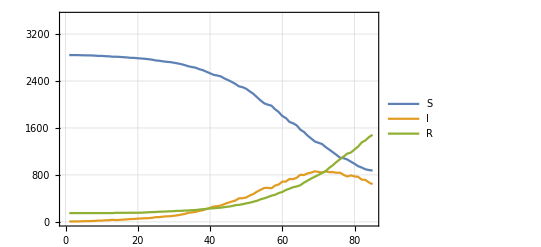

```mathematica
ListLinePlot[Values@SE0,PlotStyle->{Thick},PlotLegends->Slab,PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold}]
```

```mathematica
SE2=SEI@Hib2
```

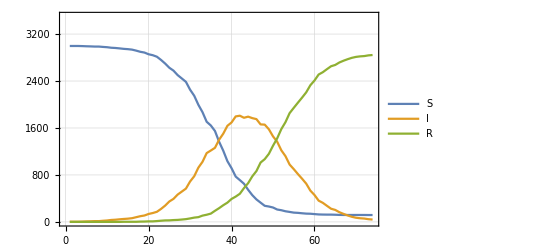

```mathematica
ListLinePlot[Values@SE2,PlotStyle->{Thick},PlotLegends->Slab,PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold}]
```

#### Run ensemble

```mathematica
(*20 week ensemble*)
HiM=
ParallelTable[
(FoldList[
CoM[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).1,(*dorm *).12,(*social*).08,(*class distance [m]*)2.5}]&,
InC,
WeR@20]),
{16}];//AbsoluteTiming
```

{658.91,Null}

```mathematica
(*All ensemble histories*)SEir=SEI/@Hin;
SEa=Merge[SEir,#&];
```

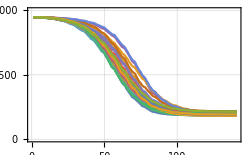
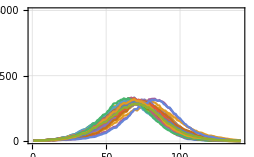
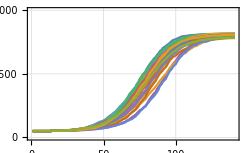
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold},PlotRange->{0,3000}]&/@SEa
```

```mathematica
(*Quantile envelop*)
SEq=Thread/@(Quantile[#,{.05,.5,.95}]&/@SEa);
```

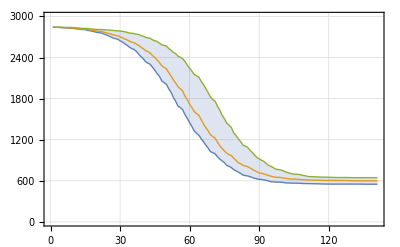
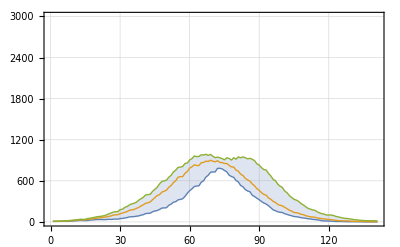
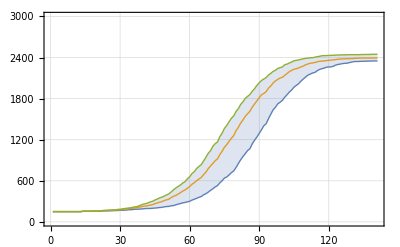
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
ListLinePlot[#,PlotStyle->{Thin,Thick,Thin},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->14,Filling->{1->{3}},PlotRange->{0,3000}]&/@SEq
```

### Quarantine code

```mathematica
(*community run with symptomatic quarantine*)
CoMQ[{(*WPool infection state*)WPool_,(*qurantine pool*)QPool_,
(*qurantine incidence #*)Qinc_,(*campus Q-count*)Qcount_},
(*scheduled classes with seats*)ClaSh_,
(*week day*)wd_,
(*dorm units*)HSU_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_,d_},
(*Q- fraction*)fQ_]:=
Block[
{splitW,splitQ,Spool,EIpo,Rpo,alS,WtQ,QtW,UWP,UQP,UWK,UHS,weekdayClasses,ClassMS,DinMS,DorMS,SPsurv,Sprog,SPInf,eiW,eiQ},
(*W-split by infection state*)splitW=GroupBy[WPool,#[[1]]&];
(*S-I,R-pools*){Spool,EIpo,Rpo}=(splitW/@{0,1,2}/.Missing[__]-><||>);
(*W-split by infection state*)splitQ=GroupBy[QPool,#[[1]]&];
(*Symptomatic cases*)alS=Select[EIpo,(#[[3]]=="S"&&#[[2]]>(*Symptom day*)5)&];
(*W->Q pool via random tests draw*)
WtQ=If[alS==<||>,<||>,<|RandomSample[alS,Round[fQ Length@alS]]|>];
(*Q -> W*)QtW=(splitQ@2/.Missing[__]-><||>);
(*Updated R-pool*)Rpo=AssociateTo[Rpo,QtW];
(*Updated EI-pool*)EIpo=Complement[EIpo,WtQ];
(*Updated WPool*)UWP=Join[Complement[WPool,WtQ],QtW];
(*Updated QPool*)UQP=Join[Complement[QPool,QtW],WtQ];
(*Current working pool keys*)UWK=Keys@UWP;
(*Updated housing*)
UHS=Intersection[UWK,#]&/@HSU;
(*Continued community run with reshuffled W,Q*)
(*Select weekday classes*)
weekdayClasses=#[[2;;]]&/@Select[ClaSh,MemberQ[#[[1]],wd]&];
(*class mixing survival*)
ClassMS=Merge[Values@(PrS[#[[1]],UWP,aC,d]&/@weekdayClasses),Times@@#&];
(*dorm mixing survival*)
DorMS=If[HSU==<||>,<||>,Union@@(PrH[#,Spool,EIpo,aD]&/@UHS)];
(*dining/social survival*)
DinMS=Union@@(PrH[#,Spool,EIpo,aS]&/@(*random mixing pools*)RMT[UWK,miP]);
(*S-pool survival prob in all environments*)SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->E transition assoc*)Sprog=(RanBernDraw/@(1-SPsurv));
(*Combined S-infection*) SPInf=Merge[{Spool,Sprog},(*S-progress function*)SProgF];
(*Complete student body progress: S-EIR terminal state*)
(*disease progress/recovery in WP*)
eiW=GroupBy[EIpo,UnitStep[#[[2]]-L@#[[3]]]&];
(*disease progress/recovery in QP*)
eiQ=GroupBy[UQP,UnitStep[#[[2]]-L@#[[3]]]&];{(*WP*)Join[SPInf,(*I-progress*)ProG/@(eiW@0/.Missing[__]-><||>),(*I-recovery*)ReC/@(eiW@1/.Missing[__]-><||>),Rpo],
(*QP*)Join[(*I-progress*)ProG/@(eiQ@0/.Missing[__]-><||>),(*I-recovery*)ReC/@(eiQ@1/.Missing[__]-><||>)],
(*QP incidence*)Length@WtQ,
(*QP-count*)Length@UQP}]
```

### Run quarantine

#### Single step

```mathematica
(*Initial state*)
InC=
(SeedRandom["Init"];IniT[StuB,.3,.05,3]);
(*Mixing pattern*)
mixP=MixP[ffp={6,4,2,1.},({2,3,4,5})]
```

{0.461538,0.307692,0.153846,0.0769231}→{2,3,4,5}

```mathematica
(*Extended inintial state*)
ExIn={InC,<||>,0,0};
```

```mathematica
(*Single step: day 1*)
in2=CoMQ[ExIn,CompCS,"W",HUass,(*random disjunct*)RanMixN,mixP,(*env risk*){.3,.3,.3,(*dist*)3},
(*Q- fractions*).7];
{KeySort@CountsBy[Values@in2[[1]],#[[1]]&],Rest@in2}
```

{<|0→2847,1→3,2→150|>,{<||>,0,0}}

```mathematica
(*repeated steps*)
in2=
CoMQ[in2,CompCS,
RandomChoice[Week],HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
{.3,.3,.3,3},
(*Q- fractions*).7];
{KeySort@CountsBy[Values@in2[[1]],#[[1]]&],Rest@in2}
```

{<|0→2846,1→4,2→150|>,{<||>,0,0}}

#### Run history

```mathematica
(*5 week history for reduced class sizes: using Rang-mixing*)
Hiq=FoldList[
CoMQ[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).3,(*dorm *).2,(*social*).25,(*class distance [m]*)3},.7]&,
ExIn,
WeR@10];//AbsoluteTiming
```

{51.0167,Null}

```mathematica
(*Split out puts*)
{His,Qhi,Qih,Qch}=Thread@Hiq;
```

```mathematica
(*Q-incidence*)Qih
```

{0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,2,1,0,1,1,3,4,5,2,4,12,10,13,15,23,13,12,27,34,39,28,50,25,18,52,64,55,43,43,23,18,26,34,33,18,20,6,2,6,4,6,4,3,1,3,3,2,1,0,0,0,0}

```mathematica
(*Q-counts*)Qch
```

{0,0,0,0,0,0,0,1,1,1,1,1,2,2,2,2,2,2,3,5,6,6,7,7,10,14,19,21,24,36,46,59,74,97,108,118,145,179,217,243,290,311,323,374,434,473,507,535,543,534,551,574,573,554,533,516,458,450,439,378,314,266,228,188,177,163,135,97,65,53,33}

#### Change mix

```mathematica
mixP2=MixP[{3,2,1,.5},{2,3,4,5}];
```

```mathematica
(*5 week history for reduced class sizes: using Rang-mixing*)
Hiq2=FoldList[
CoMQ[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP2,
(*environmental risk*){(*class*).3,(*dorm *).2,(*social*).25,(*class distance [m]*)3},.7]&,
ExIn,
WeR@10];//AbsoluteTiming
```

{50.1147,Null}

```mathematica
(*Split out puts*)
{His2,Qhi,Qih,Qch}=Thread@Hiq2;
```

```mathematica
(*Q-incidence*)Qih
```

{0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,4,3,1,1,1,1,6,5,7,6,6,4,6,10,13,19,19,28,17,11,41,42,43,43,55,24,22,56,68,50,41,48,20,15,21,24,19,15,7,4,4,4,6,1,2,1,1,1,0,0,0,0,0,0,0}

```mathematica
(*Q-counts*)Qch
```

{0,0,0,0,0,0,0,1,1,1,1,1,2,3,4,5,9,12,13,14,15,16,22,26,33,39,45,49,53,63,75,92,107,132,149,158,198,239,275,313,360,379,394,447,508,547,573,600,601,584,593,608,573,546,509,471,414,408,392,323,252,210,175,125,116,103,80,55,38,24,21}

#### Analysis

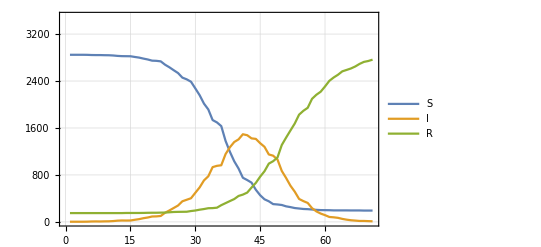

```mathematica
(*mixP*)SE0=SEI@His;
ListLinePlot[Values@SE0,PlotStyle->{Thick},PlotLegends->{"S","I","R"},PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold}]
```

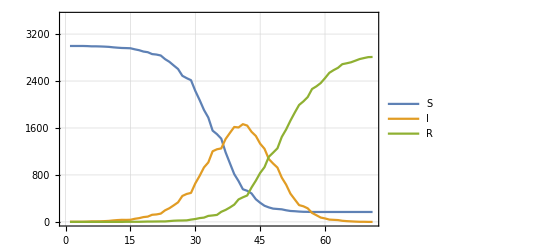

```mathematica
(*mixP2*)SE2=SEI@His2;
ListLinePlot[Values@SE2,PlotStyle->{Thick},PlotLegends->{"S","I","R"},PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold}]
```

Increased contacts (mixP2) have marginal effect on history ?

#### Run ensemble

```mathematica
HiM=
ParallelTable[
(FoldList[
CoMQ[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).3,(*dorm *).2,(*social*).3,(*class distance [m]*)3},.7]&,
ExIn,
Join[WeR@10,{"M","T","W"}]]),
{16}];//AbsoluteTiming
```

{512.705,Null}

```mathematica
(*WP ensemble histories*)SEir=SEI/@HiM[[;;,;;,1]];
SEa=Merge[SEir,#&];
```

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold},PlotRange->All]&/@SEa
```

```mathematica
(*QP ensemble histories*)SEir=SEI/@HiM[[;;,;;,2]];
SEa=Merge[SEir,#&]
```

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold},PlotRange->All]&/@SEa
```

```mathematica
out1=OutP/@HiM
```

```mathematica
SmoothHistogram/@Thread[out1]
```

Seems more organized

```mathematica
(*Quantile envelop*)
SEq=Thread/@(Quantile[#,{.05,.5,.95}]&/@SEa);
```

```mathematica
ListLinePlot[#,PlotStyle->{Thin,Thick,Thin},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->14,Filling->{1->{3}},PlotRange->All]&/@SEq
```

### Quarantine + screening

For quarantine selection: first random screening of WP, then symptomatic selection

```mathematica
(*sigmoid for test*)
Sig[x_]=x/(1+x);
(*Test sensitivity function of infectivity = x*)
TSF[(*infecivity threshold*)it_,(*steepness*)p_]=Sig[(#/it)^p]&;
```

```mathematica
(*community run with symptomatic quarantine*)
CoMQS[{(*WPool infection state*)WPool_,(*qurantine pool*)QPool_,
(*qurantine incidence #*)Qinc_,(*campus Q-count*)Qcount_},
(*scheduled classes with seats*)ClaSh_,
(*week day*)wd_,
(*dorm units*)HSU_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_,d_},
(*Q- fraction*)fQ_,
(*sreening inputs*)
{(*# daily tests*)nTT_,(*test sensitivity*)tS_,(*test Hill exponent/steepness*)pT_}]:=
Block[
{screnWP,posTW,tWtQ,NonsWP,splitW,splitQ,Spool,EIpo,Rpo,alS,WtQ,QtW,UWP,UQP,UWK,UHS,weekdayClasses,ClassMS,DinMS,DorMS,SPsurv,Sprog,SPInf,eiW,eiQ},
(*screening*)
(*screened hosts*)
screnWP=RandomSample[WPool,nTT];
(*Positive tests to Q*)
posTW=Keys@Select[RanBernDraw@TSF[(*test sensitivity*)tS,(*Hill exponent*)pT]@((*Infectivity of screenWP*)inF/@screnWP),#==1&];tWtQ=KeyTake[screnWP,posTW];(*not screened + negative tests*)
NonsWP=Complement[WPool,tWtQ];
(*W-split by infection state*)splitW=GroupBy[NonsWP,#[[1]]&];
(*S-I,R-pools*){Spool,EIpo,Rpo}=(splitW/@{0,1,2}/.Missing[__]-><||>);
(*Q-split by infection state*)splitQ=GroupBy[QPool,#[[1]]&];
(*Symptomatic cases*)alS=Select[EIpo,(#[[3]]=="S"&&#[[2]]>(*Symptom day*)5)&];
(*W->Q pool via random symptom selection*)
WtQ=If[alS==<||>,<||>,<|RandomSample[alS,Round[fQ Length@alS]]|>];
(*Q -> W*)QtW=(splitQ@2/.Missing[__]-><||>);
(*Updated R-pool*)Rpo=AssociateTo[Rpo,QtW];
(*Updated EI-pool*)EIpo=Complement[EIpo,WtQ];
(*Updated WPool*)UWP=Join[Complement[NonsWP,WtQ],QtW];
(*Updated QPool*)UQP=Join[Complement[QPool,QtW],WtQ,tWtQ];
(*Current working pool keys*)UWK=Keys@UWP;
(*Updated housing*)
UHS=Intersection[UWK,#]&/@HSU;
(*Continued community run with reshuffled W,Q*)
(*Select weekday classes*)
weekdayClasses=#[[2;;]]&/@Select[ClaSh,MemberQ[#[[1]],wd]&];
(*class mixing survival*)
ClassMS=Merge[Values@(PrS[#[[1]],UWP,aC,d]&/@weekdayClasses),Times@@#&];
(*dorm mixing survival*)
DorMS=If[HSU==<||>,<||>,Union@@(PrH[#,Spool,EIpo,aD]&/@UHS)];
(*dining/social survival*)
DinMS=Union@@(PrH[#,Spool,EIpo,aS]&/@(*random mixing pools*)RMT[UWK,miP]);
(*S-pool survival prob in all environments*)SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->E transition assoc*)Sprog=(RanBernDraw/@(1-SPsurv));
(*Combined S-infection*) SPInf=Merge[{Spool,Sprog},(*S-progress function*)SProgF];
(*Complete student body progress: S-EIR terminal state*)
(*disease progress/recovery in WP*)
eiW=GroupBy[EIpo,UnitStep[#[[2]]-L@#[[3]]]&];
(*disease progress/recovery in QP*)
eiQ=GroupBy[UQP,UnitStep[#[[2]]-L@#[[3]]]&];{(*WP*)Join[SPInf,(*I-progress*)ProG/@(eiW@0/.Missing[__]-><||>),(*I-recovery*)ReC/@(eiW@1/.Missing[__]-><||>),Rpo],
(*QP*)Join[(*I-progress*)ProG/@(eiQ@0/.Missing[__]-><||>),(*I-recovery*)ReC/@(eiQ@1/.Missing[__]-><||>)],
(*QP incidence*)Length@WtQ,
(*QP-count*)Length@UQP}]
```

### Screening steps

```mathematica
(*screened fraction of 7%/day*)
.07 3000
```

210.

```mathematica
(*day 30 state*)
{cwp,cqp,qp,qi}=Hiq[[30]];
```

```mathematica
Length/@{cwp,cqp}
```

{2964,36}

```mathematica
(*screened fraction*)
screnWP=RandomSample[cwp,210];
(*Positive tests to Q*)
posTW=Keys@Select[RanBernDraw@TSF[.1,6]@((*Infectivity of screenWP*)inF/@screnWP),#==1&];
tWtQ=KeyTake[screnWP,posTW];
(*not screened + negative test*)
NonsWP=Complement[cwp,tWtQ]
```

```mathematica
Length/@{cwp,tWtQ,NonsWP}
```

{2964,19,2945}

```mathematica
(*splitting of non-screened WP*)
splitNW=GroupBy[NonsWP,#[[1]]&];
```

```mathematica
(*splitting of screened WP*)
splitSW=GroupBy[screnWP,#[[1]]&]
```

<|0→<|F1062→{0,S},S1081→{0,S},S819→{0,S},F1489→{0,S},F231→{0,S},S499→{0,A},F1634→{0,S},F135→{0,A},F1263→{0,A},S89→{0,A},S72→{0,A},S394→{0,S},F538→{0,S},S570→{0,A},F1269→{0,A},S60→{0,S},F72→{0,A},S1144→{0,A},S276→{0,A},F1774→{0,A},S999→{0,S},F1256→{0,A},F5→{0,A},S969→{0,A},F1616→{0,A},F1098→{0,A},F1733→{0,A},F1011→{0,A},F327→{0,A},F1486→{0,A},S444→{0,A},F1279→{0,A},S458→{0,A},S477→{0,A},S1097→{0,A},F911→{0,A},S711→{0,A},F1178→{0,A},F145→{0,S},F1218→{0,S},F1786→{0,A},F786→{0,A},S678→{0,A},S556→{0,S},S318→{0,A},F444→{0,A},F1700→{0,A},F954→{0,S},F824→{0,A},F1341→{0,A},F111→{0,A},S768→{0,A},F1133→{0,A},S1070→{0,S},S614→{0,A},F1144→{0,A},F1072→{0,A},F1795→{0,A},S1121→{0,S},S543→{0,A},S334→{0,A},F282→{0,A},S240→{0,S},F1344→{0,A},F1166→{0,A},F226→{0,S},F902→{0,S},F74→{0,S},S178→{0,A},S33→{0,A},S227→{0,A},S971→{0,A},S193→{0,A},F651→{0,S},S1171→{0,S},S1096→{0,S},F921→{0,A},S61→{0,A},S690→{0,S},F421→{0,S},S639→{0,A},S866→{0,S},S83→{0,A},F1627→{0,A},S828→{0,S},F1373→{0,A},S733→{0,A},S1087→{0,S},F138→{0,A},S540→{0,A},F969→{0,A},S942→{0,A},F1792→{0,S},S168→{0,A},F168→{0,A},F29→{0,A},F1467→{0,A},F875→{0,A},S518→{0,A},F868→{0,S},S901→{0,A},F380→{0,S},F1566→{0,A},S485→{0,A},F1578→{0,A},F64→{0,S},F1788→{0,A},S814→{0,S},F604→{0,A},F1301→{0,S},F1401→{0,S},S453→{0,S},F1633→{0,S},F795→{0,A},S239→{0,A},F418→{0,A},F1243→{0,S},F253→{0,A},F1514→{0,A},S781→{0,A},S95→{0,A},F668→{0,S},F839→{0,A},S945→{0,S},F1128→{0,S},F1688→{0,S},S76→{0,A},F991→{0,A},F773→{0,A},F669→{0,A},F426→{0,A},F1259→{0,A},S26→{0,A},F1528→{0,A},F872→{0,A},S330→{0,S},F291→{0,A},S610→{0,A},S1152→{0,S},S824→{0,A},S352→{0,A},S583→{0,A},S1106→{0,S},S382→{0,A},F78→{0,A},F621→{0,A},F1224→{0,S},F1687→{0,S},F1339→{0,A},F120→{0,S},S390→{0,A},S1170→{0,A},S101→{0,S},S255→{0,S},F126→{0,A},F1619→{0,A},F256→{0,A},F262→{0,A}|>,1→<|S228→{1,6,A},F1250→{1,4,A},F856→{1,5,A},F394→{1,6,S},F1159→{1,3,A},F293→{1,6,A},F1281→{1,5,A},F14→{1,7,A},S722→{1,1,S},S1123→{1,0,A},F1116→{1,3,S},F614→{1,5,A},S832→{1,5,A},S1080→{1,0,A},S21→{1,0,S},F637→{1,11,A},S784→{1,7,A},S1167→{1,1,A},F857→{1,11,A},S734→{1,10,A},F21→{1,0,S},F588→{1,0,S},F1575→{1,5,A},S1194→{1,7,A},S78→{1,0,A},S957→{1,4,A},F693→{1,2,S},F361→{1,5,A},F1449→{1,3,A},S992→{1,1,A},S1082→{1,0,A},F1157→{1,2,A},F1546→{1,6,A},F1244→{1,4,A},F1101→{1,5,A},S860→{1,0,A},S350→{1,4,A},S757→{1,4,A},F1436→{1,0,A},F155→{1,2,A},F36→{1,0,S}|>,2→<|F770→{2,A},S650→{2,A},F1018→{2,A},S1057→{2,A},F1749→{2,A},F1148→{2,A},F1784→{2,A},F567→{2,A},F508→{2,A},S34→{2,A},S119→{2,A}|>|>

### Run quarantine+ screening

```mathematica
(*Initial state*)
InC=
(SeedRandom["Init"];IniT[StuB,.3,.05,3]);
(*Mixing pattern*)
mixP=MixP[ffp={6,4,2,1.},({2,3,4,5})];
```

```mathematica
(*Extended inintial state*)
ExIn={InC,<||>,0,0};
```

#### Single step

```mathematica
(*Single step: day 1*)
in2=CoMQS[ExIn,CompCS,"W",HUass,(*random disjunct*)RanMixN,mixP,(*env risk*){.3,.3,.3,(*dist*)3},
(*symptomatic Q- fractions*).7,
(*screen inputs*){210,.07,6}];
{KeySort@CountsBy[Values@in2[[1]],#[[1]]&],Rest@in2}
```

{<|0→2847,1→3,2→150|>,{<||>,0,0}}

```mathematica
(*repeated steps*)
in2=
CoMQS[in2,CompCS,
RandomChoice[Week],HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
{.3,.3,.3,3},
(*Symptomatic fractions*).7,
(*screen inputs*){210,.07,6}];
{KeySort@CountsBy[Values@in2[[1]],#[[1]]&],Rest@in2}
```

{<|0→2844,1→6,2→150|>,{<||>,0,0}}

#### Run history

```mathematica
(*5 week history for reduced class sizes: using Rang-mixing*)
HiS=FoldList[
CoMQS[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).3,(*dorm *).2,(*social*).25,(*class distance [m]*)3},
(*Symptomatic fractions*).7,
(*screen inputs*){210,.07,6}]&,
ExIn,
WeR@10];//AbsoluteTiming
```

{48.183,Null}

```mathematica
(*Split out puts*)
{His,Qhi,Qih,Qch}=Thread@HiS;
```

```mathematica
(*Q-incidence*)Qih
```

{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,3,2,1,1,3,4,4,1,3,2,2,7,7,6,6,11,6,5,10,16,22,18,23,13,14,23,19,25,18,26,11,8,20,25,19,13,16,6,5,9,7,4,5,6,4,1}

```mathematica
(*Q-counts*)Qch
```

{0,0,0,0,0,0,0,1,1,2,2,3,3,3,6,8,8,9,11,11,14,15,16,17,18,21,25,29,36,43,53,56,64,70,79,87,104,125,129,149,169,193,216,231,273,292,321,344,391,439,488,535,569,609,645,662,668,674,689,673,648,597,595,575,554,517,459,424,365,334,284}

#### Analysis: Screening vs. symptomatic Q

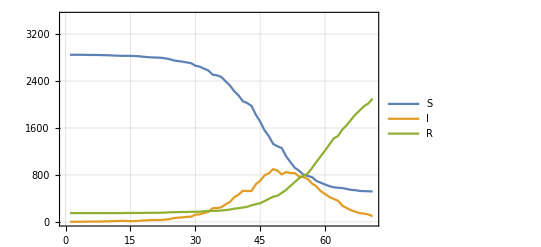

```mathematica
(*mixP*)SE0=SEI@His;
ListLinePlot[Values@SE0,PlotStyle->{Thick},PlotLegends->{"S","I","R"},PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold}]
```

symptomatic

-Graphics-

#### Run ensemble

```mathematica
HiM=
ParallelTable[
(FoldList[
CoMQ[#,(*classes*)CompCS,
(*week day*)#2,
(*Housing*)HUass,
(*random nonoverlap*)RanMixN,(*pattern*)mixP,
(*environmental risk*){(*class*).3,(*dorm *).2,(*social*).3,(*class distance [m]*)3},.7]&,
ExIn,
Join[WeR@10,{"M","T","W"}]]),
{16}];//AbsoluteTiming
```

{512.705,Null}

```mathematica
Dimensions@HiM
```

{16,74,4}

```mathematica
(*WP ensemble histories*)SEir=SEI/@HiM[[;;,;;,1]];
SEa=Merge[SEir,#&];
```

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold},PlotRange->All]&/@SEa
```

```mathematica
(*QP ensemble histories*)SEir=SEI/@HiM[[;;,;;,2]];
SEa=Merge[SEir,#&]
```

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->{14,Bold},LabelStyle->{Black,Bold},PlotRange->All]&/@SEa
```

```mathematica
out1=OutP/@HiM
```

```mathematica
SmoothHistogram/@Thread[out1]
```

Seems more organized

```mathematica
(*Quantile envelop*)
SEq=Thread/@(Quantile[#,{.05,.5,.95}]&/@SEa);
```

```mathematica
ListLinePlot[#,PlotStyle->{Thin,Thick,Thin},Frame->True,PlotTheme->"Detailed",FrameStyle->{Black,Bold},BaseStyle->14,Filling->{1->{3}},PlotRange->All]&/@SEq
```